```mathematica
<<MaTeX`
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color,txfonts,amsbsy}"}];
<<ErrorBarLogPlots`
(* Plotting Package *)
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color,txfonts}"}];
rasterListContourPlot[pList_,opts:OptionsPattern[]]:=Module[{img,cont,contL,plotRangeRule,contourOptions,frameOptions,rangeCoords},contourOptions=Join[FilterRules[{opts},FilterRules[Options[ListContourPlot],Except[{Background,Frame,Axes}]]],{Frame->None,Axes->None}];
contL=ListContourPlot[pList,Evaluate@Apply[Sequence,contourOptions]];
cont=First[Cases[{contL},Graphics[__],Infinity]];
img=Rasterize[Graphics[GraphicsComplex[cont[[1,1]],cont[[1,2,1]]],PlotRangePadding->None,ImagePadding->None,Options[cont,PlotRange]],"Image",ImageSize->With[{size=Total[{2,0} (ImageSize/.{opts})/.{ImageSize->CurrentValue[ImageSize]}]},If[NumericQ[size],size,First[WindowSize/.Options[EvaluationNotebook[]]]]]];
plotRangeRule=FilterRules[AbsoluteOptions[cont],PlotRange];
rangeCoords=Transpose[PlotRange/.plotRangeRule];
frameOptions=Join[FilterRules[{opts},FilterRules[Options[Graphics],Except[{PlotRangeClipping,PlotRange}]]],{plotRangeRule,Frame->True,PlotRangeClipping->True}];
If[Head[contL]===Legended,Legended[#,contL[[2]]],#]&@Show[Graphics[{Inset[Show[SetAlphaChannel[img,"ShadingOpacity"/.{opts}/.{"ShadingOpacity"->1}],AspectRatio->Full],rangeCoords[[1]],{0,0},rangeCoords[[2]]-rangeCoords[[1]]]},PlotRangePadding->None],Graphics[GraphicsComplex[cont[[1,1]],cont[[1,2,2]]]],Evaluate@Apply[Sequence,frameOptions]]]
(* These functions can basically be ignored. It's just dealing with the graphics for when I want to format my publication-quality plots. *)
Clear[undistortedGraphicsColumn];
Options[undistortedGraphicsColumn]=Join[{Spacings->0},Options[Graphics]];
undistortedGraphicsColumn[list_, opts:OptionsPattern[]]:=Module[{sizes=ImageDimensions/@list,width, xsizes, ysizes},width=Max@sizes[[All,1]];
ysizes=sizes[[All,2]]+Join[{0},ConstantArray[OptionValue[Spacings],Length@list-1]];
xsizes = sizes[[All, 1]];
Graphics[Table[Inset[list[[i]],{(width - xsizes[[i]]) / 2,-Plus@@ysizes[[;;i]]},ImageScaled[{0,0}]],{i,Length[list]}],ImageSize->{width,Plus@@ysizes},ImagePadding->None,PlotRange->{{0,width},{-Plus@@ysizes,0}},AspectRatio->Plus@@ysizes/width,PlotRangePadding->None]]

Clear[undistortedGraphicsRow];
Options[undistortedGraphicsRow]=Join[{Spacings->0},Options[Graphics]];
undistortedGraphicsRow[list_, opts:OptionsPattern[]]:=Module[{sizes=ImageDimensions/@list,height, xsizes, ysizes},height=Max@sizes[[All,2]];
xsizes=sizes[[All,1]]+Join[ConstantArray[OptionValue[Spacings],Length@list-1],{0}];
ysizes = sizes[[All, 2]];
Graphics[Table[Inset[list[[i]],{If[i>1, Plus@@xsizes[[;;i-1]],0], (height-ysizes[[i]])/2},ImageScaled[{0,0}]],{i,Length[list]}],ImageSize->{Plus@@xsizes, height},ImagePadding->None,PlotRange->{{0, Plus@@xsizes}, {0, height}},AspectRatio->height/(Plus@@xsizes),PlotRangePadding->None]]

Clear[format]
Options[format] = Options[PaddedForm];
format[x_, sd_]:=Module[{m,e},
{m,e} = MantissaExponent[x];
If[x == 0, "0",If[-2≤e≤2,ToString[PaddedForm[x, sd]],ToString[PaddedForm[ToExpression[ToString[m]]*10, sd]]<>"\\times10^{"<>ToString[e-1]<>"}"]]
]
```

```mathematica
(*Current fluctuations lower bound*)
<<ErrorBarLogPlots`
DissipationAna=Import[NotebookDirectory[]<>"../../data/FiveDtiltedLB.mat"][[1]];
(*Changing temperature for 100 or 500*)
(*datalength varies from 12s to 12000s*)
(*Nspace is the stroboscopic size, like 50 means taking every 50 points*)
temperature=500;
datalength=1200;
count=1;
Nspace=5;
```

```mathematica
EstthermoForceCurFluc=Table[
temp=Table[
CurFluc=Flatten[Import[NotebookDirectory[]<>"../../data/BandwidthTest/CurFluc_5_"<>ToString[temperature]<>"_"<>ToString[datalength]<>"_"<>ToString[count] <>"_"<>ToString[Nspace] <>"_"<>ToString[Bscale] <>".mat"]];

dt=0.001*Nspace;
L=Length[CurFluc];
NChop=20;
Tobs=20/NChop;
thermoΔJd=Table[CurFluc[[i]] - CurFluc[[i-Tobs/dt]],{i,( 1/NChop+Tobs)/dt, L-1,1/(NChop*dt)}];
Subscript[μ, 1]=Chop[Mean[thermoΔJd]/Tobs];
Subscript[var, 1] =Tobs Variance[thermoΔJd/Tobs]; 
Σ=2 Subscript[μ, 1]^2/Subscript[var, 1]
(*Print["Temperature"<>ToString[temperature] <>" Length"<>ToString[datalength] <>" Dissipation "<>ToString[Σ] <>"."];
Σ*)
,{count,1,100}];
{Bscale,temp}
,{Bscale,{0.6,1,1.4,1.8,2.2,2.6,3}}];
```

```mathematica
Temporal=Table[
temp=Table[
CurFluc=Flatten[Import[NotebookDirectory[]<>"../../data/BandwidthTest/CurFluc_5_"<>ToString[temperature]<>"_"<>ToString[datalength]<>"_"<>ToString[count] <>"_"<>ToString[Nspace] <>"_"<>ToString[Bscale] <>".mat"]];
Σ=CurFluc[[-1]]/datalength
,{count,1,100}];
{Bscale,temp}
,{Bscale,{0.6,1,1.4,1.8,2.2,2.6,3}}];
```

```mathematica
TURMSE=Table[
temp=Table[
(Mean[EstthermoForceCurFluc[[i,2]][[10*(j-1)+1;;10*j]]]-Mean[Transpose[DissipationAna][[-1]]])^2+Variance[EstthermoForceCurFluc[[i,2]][[10*(j-1)+1;;10*j]]]
,{j,1,10}];
{EstthermoForceCurFluc[[i,1]],Mean[temp],StandardDeviation[temp]/Sqrt[10]}
,{i,1,7}];
```

```mathematica
TemporalMSE=Table[
temp=Table[
(Mean[Temporal[[i,2]][[10*(j-1)+1;;10*j]]]-Mean[Transpose[DissipationAna][[-1]]])^2+Variance[Temporal[[i,2]][[10*(j-1)+1;;10*j]]]
,{j,1,10}];
{EstthermoForceCurFluc[[i,1]],Mean[temp],StandardDeviation[temp]/Sqrt[10]}
,{i,1,7}];
```

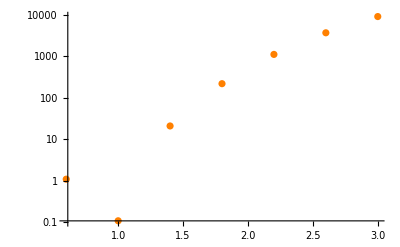

```mathematica
ErrorListLogPlot[TemporalMSE,PlotStyle-> Orange]
```

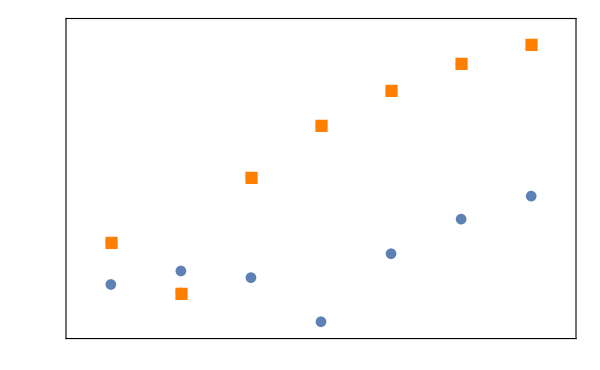

```mathematica
ymax = 3;
ymajor = 1;
yminor = 0.1;
ticksize = 18;
SIfig1=Show[
ErrorListLogPlot[TURMSE],
ErrorListLogPlot[TemporalMSE,PlotStyle-> Orange],
ErrorListLogPlot[TemporalMSE,PlotMarkers->{{■,16}},PlotStyle->Orange],
FrameTicks-> {
Join[
Table[{i, MaTeX[i, FontSize->ticksize], {0.01,0}}, {i, 0,ymax, ymajor}],
Table[{i, "", 0.005}, {i, 0, ymax, yminor}]
],
Join[
{
{Log[0.01], MaTeX["10^{-2}", FontSize->ticksize], {0.01,0}},
{Log[0.1], MaTeX["10^{-1}", FontSize->ticksize], {0.01,0}},
{Log[1], MaTeX["1", FontSize->ticksize], {0.01,0}},
{Log[10], MaTeX["10^1", FontSize->ticksize], {0.01,0}},
{Log[100], MaTeX["10^2", FontSize->ticksize],  {0.01,0}},
{Log[1000], MaTeX["10^3", FontSize->ticksize],  {0.01,0}},
{Log[10000], MaTeX["10^4", FontSize->ticksize],  {0.01,0}}
},
Table[{Log[i 0.01],"", {0.005,0}},{i, 5, 9, 1}],
Table[{Log[i 0.1],"", {0.005,0}},{i, 5, 9, 1}],
Table[{Log[i 1],"", {0.005,0}},{i, 5, 9, 1}],
Table[{Log[i 10],"", {0.005,0}},{i, 1, 9, 1}],
Table[{Log[i 100],"", {0.005,0}},{i, 1, 9, 1}],
Table[{Log[i 1000],"", {0.005,0}},{i, 1, 9, 1}],
Table[{Log[i 10000],"", {0.005,0}},{i, 1, 2, 1}]
],
Join[
Table[{i, "", {0.01,0}}, {i, 0, ymax, ymajor}],
Table[{i, "",{0.005,0}}, {i, 0, ymax, yminor}]
], 
Join[
{
{Log[0.01], "", {0.01,0}},
{Log[0.1], "", {0.01,0}},
{Log[1], "", {0.01,0}},
{Log[10], "", {0.01,0}},
{Log[100],"",{0.01,0}},
{Log[1000], "", {0.01,0}},
{Log[10000], "", {0.01,0}}
},
Table[{Log[i 0.01],"",{0.005,0}},{i, 5, 9, 1}],
Table[{Log[i 0.1],"",{0.005,0}},{i, 5, 9, 1}],
Table[{Log[i 1],"",{0.005,0}},{i, 5, 9, 1}],
Table[{Log[i 10],"", {0.005,0}},{i, 1, 9, 1}],
Table[{Log[i 100],"", {0.005,0}},{i, 1, 9, 1}],
Table[{Log[i 1000],"", {0.005,0}},{i, 1, 9, 1}],
Table[{Log[i 10000],"", {0.005,0}},{i, 1, 2, 1}]
]
},
Epilog->{
Inset[
PointLegend[97, MaTeX[#, FontSize->16]&/@{"\\text{TUR lower bound}", "\\text{Temporal Integral}"}, LegendMarkers->{Automatic, 16}], Scaled[{0.2, 0.78}]
]
},
ImageSize-> 600,
PlotRange-> {{0.4,3.2},{-4,10}},
Frame-> True,
FrameLabel->{MaTeX["\\text{Scaled Bandwidth}",FontSize->24],MaTeX["\\text{Mean Squared Error}",FontSize->24]}
]
```

```mathematica
Export[NotebookDirectory[]<>"SIfig1.pdf", SIfig1];
Export[NotebookDirectory[]<>"../SIfig1.pdf", SIfig1];
```